```mathematica
(*DANE:*)
S = 0.1*10^-6;(*m^2*)
α = 60;
Δt = 0.002;(*s*)
```

Set::wrsym: Symbol C is Protected.

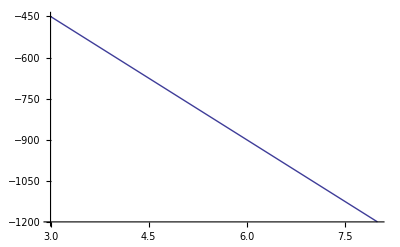

```mathematica
(*SZUKANE:*)

Pz = p;
Ppz = 0.7*p;
Pxd = Ppz - Pz;
F = Pxd/Δt;
C = F/S;
Plot[F/S, {p, 30*10^-8, 80*10^-8}]
```

```mathematica
ClearAll["Global`*"];
```

Set::wrsym: Symbol C is Protected.

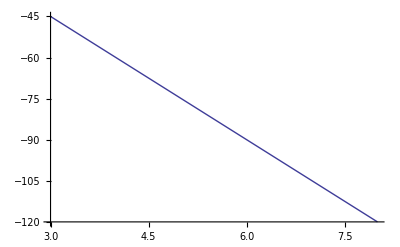

```mathematica
(*DANE:*)
S = 0.1*10^-6;(*m^2*)
α = 60;
Δt = 0.02;(*s*)
(*SZUKANE:*)

Pz = p;
Ppz = 0.7*p;
Pxd = Ppz - Pz;
F = Pxd/Δt;
C = F/S;
Plot[F/S, {p, 30*10^-8, 80*10^-8}]
```